## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170104";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
(*绘制中位数比热力图*)
PlotRatioHeatmap[results,"MedianRatios","Median Ratio Heatmap"]

(*绘制宽度比热力图*)
PlotRatioHeatmap[results,"WidthRatios","Width Ratio Heatmap"];

(*绘制下界比热力图*)
PlotRatioHeatmap[results,"LowerBoundRatios","Lower Bound Ratio Heatmap"];

(*绘制上界比热力图*)
PlotRatioHeatmap[results,"UpperBoundRatios","Upper Bound Ratio Heatmap"];
```

Error: ratioType not found in results

## m1-m2 Plot, 22

## INSPIRAL

```mathematica
plots=<||>;
compPlots=<||>;
vsPlots=<||>;
vsPlots["p2p4"]={};
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_2"}; (*换参数改这里*)
CASE="p2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0001};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.0001}，共 2 条

第一条前3点：{{8.71124,8.37584},{8.73641,8.30396},{8.78956,8.24932}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.99775

可信水平百分比：99.775%

==========================

{dphi_2} 预处理完成，红线包含概率 prob = 0.99775

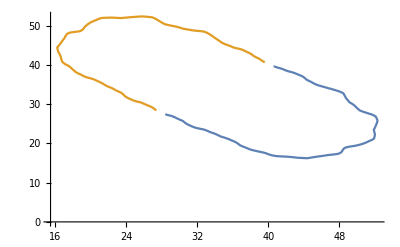

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

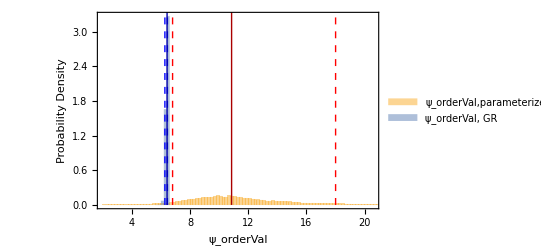

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_2}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.03785, 0.96215}

GR 目标区间: {6.25259, 6.44167}

Param 目标区间: {6.43959, 18.7291}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=3.96128×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.41753×10^-15

Param下界: 点数=500 | Y>0点数=500 | 平均误差=8.63309×10^-16

Param上界: 点数=500 | Y>0点数=500 | 平均误差=12.2873

{{10.1,9.3605},{10.2,9.45318},{10.3,9.54585},{10.4,9.63853},{10.5,9.73121}}

{{10.1,10.1011},{10.2,10.2003},{10.3,10.3004},{10.4,10.4014},{10.5,10.501}}

chi1L取值：0.459326

chi2L取值：0.4582

=====================================================

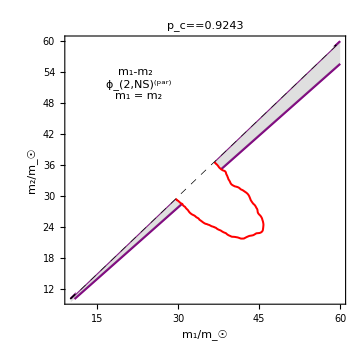

```mathematica
p={"dphi_2"}
probability=prob;
probability=0.9243;
plots[CASE]=PlotMultiInversion[p,{probability},10,60,0.1,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_4"}; (*换参数改这里*)
CASE="p4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.001455};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001455}，共 2 条

第一条前3点：{{30.0511,30.7151},{30.0272,30.7409},{29.8688,30.8727}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.93094

可信水平百分比：93.094%

==========================

{dphi_4} 预处理完成，红线包含概率 prob = 0.93094

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

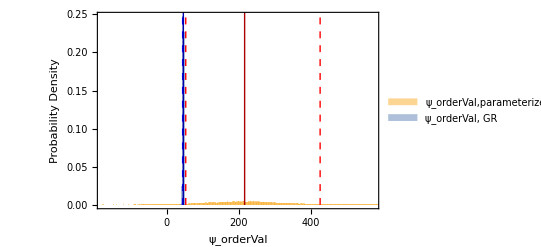

```mathematica
p={"dphi_2"}
probability=prob;
probability=0.9243;
plots[CASE]=PlotMultiInversion[p,{probability},10,60,0.1,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

{dphi_4}

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0438, 0.9562}

GR 目标区间: {43.8576, 46.244}

Param 目标区间: {46.0001, 438.983}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=5.44749×10^-15

GR上界: 点数=300 | Y>0点数=300 | 平均误差=1.02555×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=2.22637×10^-15

Param上界: 点数=300 | Y>0点数=300 | 平均误差=392.737

{{20.1,25.2916},{20.2,25.4174},{20.3,25.5432},{20.4,25.6691},{20.5,25.7949}}

{{20.1,20.101},{20.2,20.2009},{20.3,20.3013},{20.4,20.4022},{20.5,20.5036}}

chi1L取值：0.509548

chi2L取值：0.467782

=====================================================

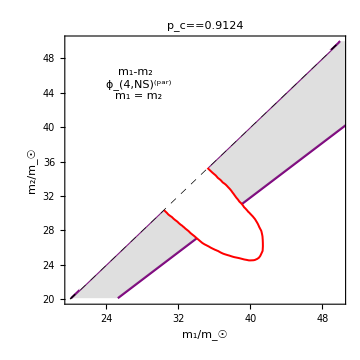

```mathematica
p={"dphi_4"}
probability=prob;
probability=0.9124;
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_5l"}; (*换参数改这里*)
CASE="p5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_5l} 预处理完成，红线包含概率 prob = 0.955895

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

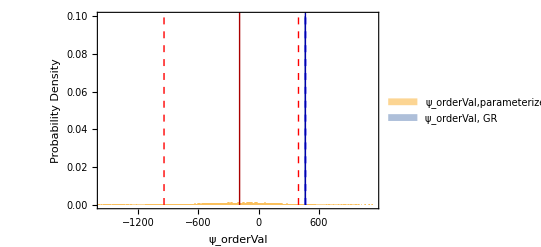

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_5l}

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0342, 0.9658}

GR 目标区间: {464.758, 466.98}

Param 目标区间: {-1049.02, 465.}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=4.62326×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.40637×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=1513.77

Param上界: 点数=300 | Y>0点数=300 | 平均误差=2.48216×10^-14

{{20.1,20.0701},{20.2,20.1722},{20.3,20.2748},{20.4,20.3778},{20.5,20.4814}}

{{20.1,25.5674},{20.2,25.6946},{20.3,25.8218},{20.4,25.949},{20.5,26.0762}}

chi1L取值：0.418848

chi2L取值：0.455312

=====================================================

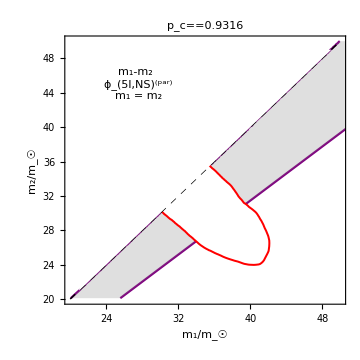

```mathematica
p={"dphi_5l"}
probability=prob;
probability=0.9316;
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_6"}; (*换参数改这里*)
CASE="p6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.001};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001}，共 2 条

第一条前3点：{{35.7844,35.1204},{35.8747,35.0531},{35.9918,34.9222}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.952061

可信水平百分比：95.2061%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.952061

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

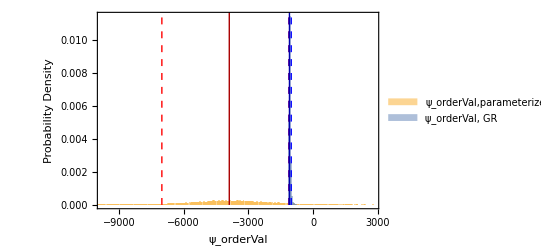

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_6}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.04915, 0.95085}

GR 目标区间: {-1103.97, -1006.56}

Param 目标区间: {-7033.68, -1102.5}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.12929×10^-13

GR上界: 点数=300 | Y>0点数=300 | 平均误差=8.94336×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=5929.55

Param上界: 点数=300 | Y>0点数=300 | 平均误差=1.53856×10^-13

{{20.1,20.0977},{20.2,20.1997},{20.3,20.2992},{20.4,20.3992},{20.5,20.4996}}

{{20.1,21.9655},{20.2,22.0748},{20.3,22.184},{20.4,22.2933},{20.5,22.4026}}

chi1L取值：0.510796

chi2L取值：0.446253

=====================================================

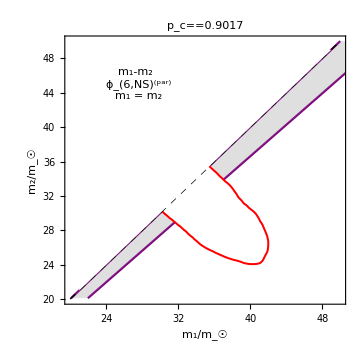

```mathematica
p={"dphi_6"}
probability=prob;
probability=0.9017;
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_7"}; (*换参数改这里*)
CASE="p7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_7} 预处理完成，红线包含概率 prob = 0.955895

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

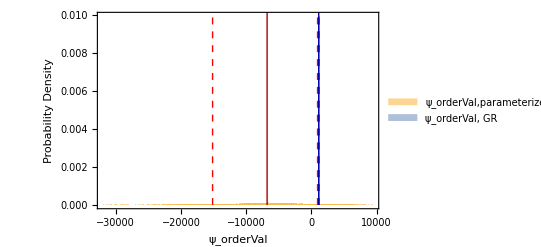

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_7}

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.047, 0.953}

GR 目标区间: {1112.67, 1130.87}

Param 目标区间: {-15343.5, 1128.21}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=9.09495×10^-15

GR上界: 点数=300 | Y>0点数=300 | 平均误差=3.03165×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=16297.2

Param上界: 点数=300 | Y>0点数=300 | 平均误差=1.40972×10^-13

{{20.1,96903.2},{20.2,97385.3},{20.3,97867.4},{20.4,98349.4},{20.5,98831.6}}

{{20.1,26.11},{20.2,26.2399},{20.3,26.3698},{20.4,26.4997},{20.5,26.6296}}

chi1L取值：0.479016

chi2L取值：0.448311

=====================================================

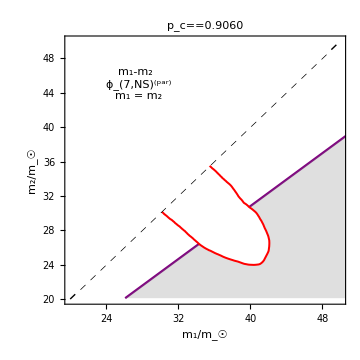

```mathematica
p={"dphi_7"}
probability=prob;
probability=0.9060;
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

```mathematica
plots
```

<|p2→-Graphics-,p4→-Graphics-,p5l→-Graphics-,p6→-Graphics-,p7→-Graphics-|>

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0438, 0.9562}

GR 目标区间: {1112.27, 1130.88}

Param 目标区间: {-15548.7, 1293.05}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=9.76369×10^-14

GR上界: 点数=170 | Y>0点数=170 | 平均误差=2.80873×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=16502.4

Param上界: 点数=170 | Y>0点数=170 | 平均误差=162.153

{{3.1,14760.1},{3.2,15236.2},{3.3,15712.3},{3.4,16188.4},{3.5,16664.6}}

{{3.1,3.10003},{3.2,3.20004},{3.3,3.29996},{3.4,3.40002},{3.5,3.50001}}

chi1L取值：0.479016

chi2L取值：0.448311

=====================================================

警告：参数 dphi_7 模式为 Points，但未提供有效 extremePointsList，已跳过。

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0438, 0.9562}

GR 目标区间: {43.8576, 46.244}

Param 目标区间: {46.0001, 438.983}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=5.0156×10^-15

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.09507×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=2.00624×10^-15

Param上界: 点数=170 | Y>0点数=170 | 平均误差=392.737

{{3.1,3.90069},{3.2,4.02652},{3.3,4.15235},{3.4,4.27818},{3.5,4.404}}

{{3.1,3.10062},{3.2,3.20068},{3.3,3.30011},{3.4,3.3993},{3.5,3.49947}}

chi1L取值：0.509548

chi2L取值：0.467782

=====================================================

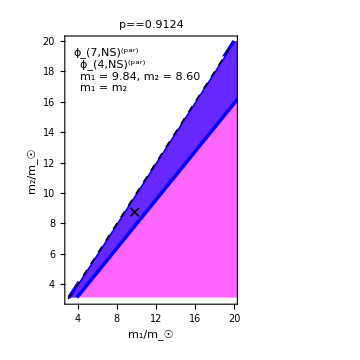

```mathematica
p={"dphi_7","dphi_4"};
probability=prob;
probability=0.9124;
(*probability=0.2;*)
PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points","Points"},
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->True]
```

# utils